```mathematica
init:=(
δt=0.01;
f=v=r=0;
fluidDensity=1;
gravity=-9.81;
);
step[radius_,mass_]:=(
(*Buoyancy*)
With[{volume=4/3 π radius^3},
f+=(fluidDensity-mass/volume)*volume;
f+=gravity*mass;
];
(*Integrate*)
v +=f*δt;
r +=v*δt;
f=0;
v*=0.97;
r
);
```

```mathematica
trajectory[radius_,mass_]:=(init;Table[step[radius,mass],50]);
```

```mathematica
trajectory[1,1]
```

{-0.000662121,-0.0019665,-0.00389387,-0.00642554,-0.00954337,-0.0132298,-0.0174678,-0.0222407,-0.0275326,-0.0333278,-0.0396113,-0.0463684,-0.0535849,-0.0612471,-0.0693415,-0.0778552,-0.0867756,-0.0960905,-0.105788,-0.115857,-0.126286,-0.137064,-0.148181,-0.159626,-0.17139,-0.183464,-0.195837,-0.208501,-0.221448,-0.234668,-0.248154,-0.261897,-0.27589,-0.290126,-0.304596,-0.319294,-0.334214,-0.349348,-0.364691,-0.380235,-0.395975,-0.411904,-0.428019,-0.444311,-0.460777,-0.477412,-0.494209,-0.511165,-0.528273,-0.545531}

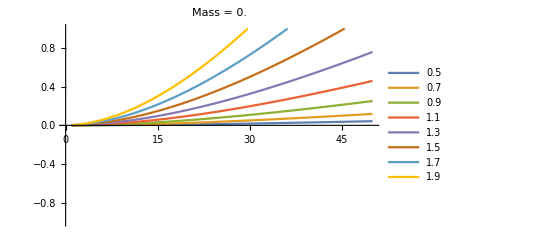
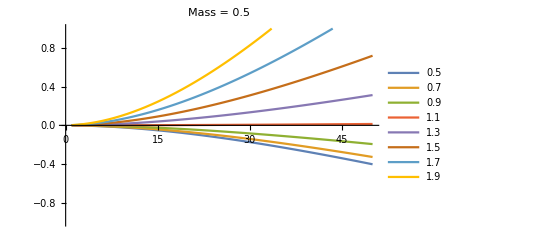
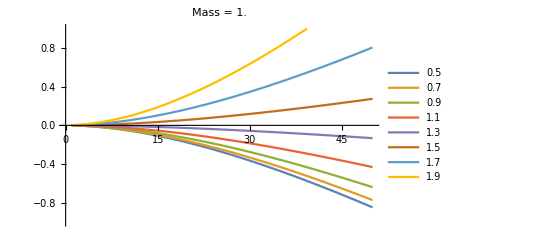
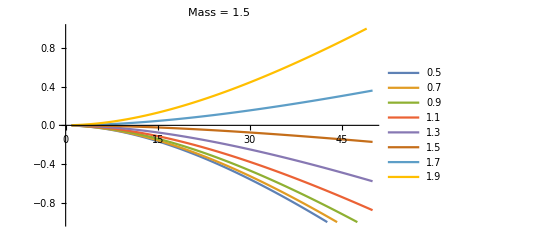
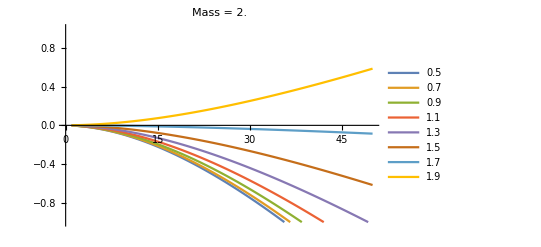
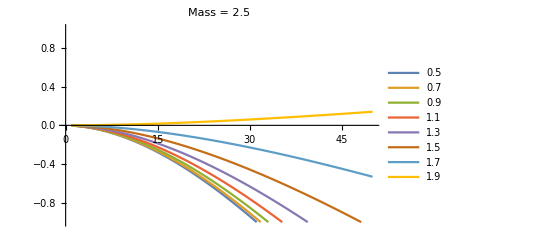
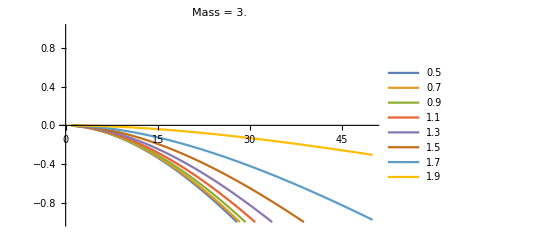
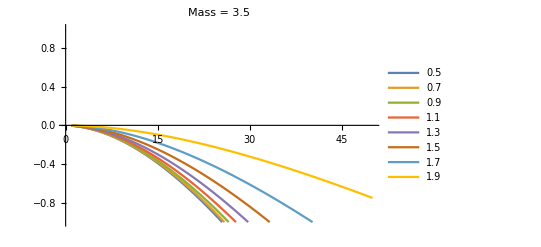

```mathematica
Table[
With[{rads=Table[radius,{radius,0.5,2,0.2}]},
ListLinePlot[trajectory[#,mass]&/@rads,PlotLegends->rads,PlotLabel->StringForm["Mass = ``",mass],PlotRange->{-1,1}]],{mass,0,4,0.5}]
```

```mathematica
ListPlot3D[Table[trajectory[#,mass],{mass,0,2*fluidDensity}]&/@{0.1,1,2*fluidDensity},AxesLabel->{"time","mass","distance"},PlotLegends->{0.1,1,2}]
```

-Graphics3D-

```mathematica
criticalRadius[mass_]:=Module[{volume=4/3 π radius^3,δv},
δv=((fluidDensity-mass/volume)*volume)+(gravity*mass);
Quiet[radius/.Solve[{δv==0,radius≤2,radius≥1/2},radius]//First]
]
```

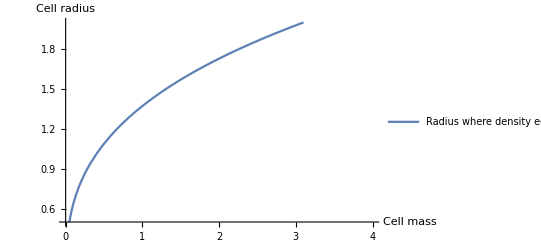

```mathematica
Plot[criticalRadius[mass],{mass,0,4}, 
AxesLabel->{"Cell mass","Cell radius"},
PlotLegends->{"Radius where density equals fluid density"}
]
```